```mathematica
Clear["Global`*"]
```

# Gravitational Waves from Exoplanets

KISS, try to Keep It Simple.

## Revisions

20160705 Start this file and keep things to a minimum.  Focus especially on the Amaro-Seoane et al. Eqn 15 for LISA.

## References

P. Amaro-Seoane et al. “Triplets of supermassive black holes: astrophysics, gravitational waves and detection,” MNRAS 402 2308-2320 (2010);
P. C. Peters and J. Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 (1963) 435-440.
Michele Maggiore, “Gravitational Waves. Volume 1: Theory and Experiments,” Oxford Univ. Press, 2008.

## Directories

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
myDir = "/home/gabella/Documents/astro/exop/";
```

## Useful constants.

Some constants.  Work in SI units.
Okay, join the astro / GR world and look at units of length for mass, etc, that is G=c=1 type of unit conversion.

```mathematica
massSun = 1.99 10^30; (*kg *)
massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = 317.9; (* earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
bigG = 6.67384 10^-11; (* Gravitational constant, m^3/kg/s *)

rscon = 2955.43; (* meters per solar mass, Schwarzschild radius *)
rscon = 2*6.67388 10^-11*massSun/cee^2 (* solar mass Scharzschild radius *)
lunits =6.67388 10^-11*massSun/cee^2 (* meters per solar mass, units of G=c=1, no factor of 2 as in Schwarzschild radius *)
masscon = 1477.71; (* m, G Msol/c^2, for 1 solar mass *)
powercon = 3.628 10^52; (* W, c^5/G, W/unit since P is dimensionless in G=c=1 units *)
energycon = 1.210 10^44; (* J/m, c^4/G *)
```

2955.43

1477.71

## Kepler motion

The orbital frequency, a is the semi-major axis if elliptical orbits, the radial separation of the masses is 2*R is circular.

```mathematica
sepAU[days_]:=(days/365.24)^(2/3)
calchzero[plorbper_, plbmassj_, stmass_, stdist_]:=
(plbmassj*massJs*rscon*stmass*rscon)/(sepAU[plorbper]*au*stdist*pc)
calcωsq[plorbper_, plbmassj_, stmass_]:=
((plbmassj*massJs+stmass)*rscon/2)/(sepAU[plorbper]*au)^3(* really (ω/c)^2, like k *)
```

## Grab and read the Exoplanet database

### URL References

From http://exoplanetarchive.ipac.caltech.edu/docs/program_interfaces.html#collists
 
wget “http://exoplanetarchive.ipac.caltech.edu/cgi-bin/nstedAPI/nph-nstedAPI?table=exoplanets&select=pl_hostname,ra,dec&order=dec&format=ascii” -O “planets.txt”

wget “http://exoplanetarchive.ipac.caltech.edu/cgi-bin/nstedAPI/nph-nstedAPI?table=exoplanets&format=csv” -O “defaults.csv” 

wget “http://exoplanetarchive.ipac.caltech.edu/cgi-bin/nstedAPI/nph-nstedAPI?table=keplertimeseries&quarter=14&format=ipac” -O “Qtr14.tbl” 

wget “http://exoplanetarchive.ipac.caltech.edu/cgi-bin/nstedAPI/nph-nstedAPI?table=keplertimeseries&kepid=8561063&format=ipac” -O “KIC8561063.tbl”

Note: Due to the large amount of metadata with Kepler releases, Kepler queries must specify a quarter. Each quarter is approximately 170 MB.
Looks like Q1 to Q16, sixteen quarters, ...&quarter=14&...

### Grab the data or read the saved CSV file.

```mathematica
exopURL="http://exoplanetarchive.ipac.caltech.edu/cgi-bin/nstedAPI/nph-nstedAPI?";
(*searchString = "table=exoplanets&select=pl_hostname,ra,dec&order=dec&format=CSV";*)
searchString="table=exoplanets&select=pl_hostname,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx&order=dec&format=CSV";
```

Do not run the URLExecute[] all the time. Do not import all the time.

```mathematica
newSearch=False;
(*newSearch = True;*)
dateTimeStamp=Block[{$DateStringFormat={"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}},DateString[]];
fileName =myDir<>"exop_"<>dateTimeStamp<>".csv"
cvsFileName = filename;
If[newSearch,
aa=URLExecute[exopURL<>searchString];, ]

If[newSearch,Export[fileName,aa, "CSV"];, ]
```

/home/gabella/Documents/astro/exop/exop_20160707_151120.csv

### Read the csv file.

```mathematica
lastGoodFile = myDir<>"exop_20160701_113512.csv"
```

/home/gabella/Documents/astro/exop/exop_20160701_113512.csv

```mathematica
If[newSearch,
bb=Import[fileName], bb = Import[lastGoodFile]];
```

```mathematica
{Length[bb],Length[bb[[1]]]} (* Rows and Columns *)
```

{3286,9}

```mathematica
bb[[1;;8]]//TableForm
```

pl_hostname | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92
HD 137388 A | 330. | 0.89 | 0.36 | 0.223 | 38.45 | 0.86 | 2014-05-14 | 26.01
GJ 3021 | 133.71 | 0.49 | 0.511 | 3.37 | 17.62 | 0.9 | 2014-05-14 | 56.76
HD 63454 | 2.81805 | 0.0368 | 0. | 0.398 | 35.8 | 0.84 | 2015-03-26 | 27.93
HD 212301 | 2.24572 | 0.036 | 0. | 0.45 | 52.72 | 1.27 | 2014-05-14 | 18.97
CHXR 73 |  | 210. |  | 12.569 |  | 0.35 | 2014-05-14 |

Data is in array bb of mixed type, some numbers, some strings, some nulls.  First row is the columns headings, rest is the data.

Convenient to create a dictionary/association of the text with the column.

```mathematica
rowHeaders=1; rowDataStart=rowHeaders+1;  (* Row with the headers, etc . *)
cols = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ bb[[rowHeaders]] ], icnt+=1,
AppendTo[cols,bb[[rowHeaders,icnt]]->icnt]
];
```

```mathematica
Keys[cols]
{cols["rowid"], cols["pl_orbper"]} (* Oops, did not grab the rowid in the URL query. *)
```

{pl_hostname,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

{Missing[KeyAbsent,rowid],2}

### Do the filtering for datafields we need for GW work.

Some of the fields are blank, so drop those planets from consideration.

```mathematica
Clear[filterBlanks2]
filterBlanks2[aa_, filterInd_]:=Module[{retList, blankList},
retList={};
blankList={};
For[i=1,i<=Length[aa], i++,
If[ NumberQ[ aa[[i,filterInd]] ], AppendTo[retList, aa[[i]] ], AppendTo[blankList, aa[[i]] ]]
];
{retList, blankList}
]
```

```mathematica
(*alldata = Import[fileName, "Data"];*)
alldata = bb;
```

```mathematica
alldata[[71;;73]] //TableForm(* Look for the row headers. *)
```

WASP-73 | 4.08722 | 0.05512 | 0. | 1.88 |  | 1.34 | 2014-05-14 | 
AB Pic |  | 260. |  | 13.5 | 45.52 |  | 2014-05-14 | 21.97
HD 30177 | 2770. | 3.95 | 0.193 | 10.45 | 54.71 | 1.01 | 2014-07-23 | 18.28

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.

```mathematica
Print["Length alldata ",Length[alldata] ]
fdata1 = filterBlanks2[alldata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "pl_orbeccen ", Length[fdata1]]
fdata2 = filterBlanks2[fdata1, cols["pl_orbper"] ][[1]]; Print[ "pl_orbper ",Length[fdata2] ]
fdata3 = filterBlanks2[fdata2, cols["pl_orbsmax"] ][[1]]; Print["pl_orbsmax ",Length[fdata3] ]
fdata4 = filterBlanks2[fdata3, cols["pl_bmassj"] ][[1]]; Print["pl_bmassj ",Length[fdata4] ] (* use pl_bmassj not pl_massj *)
fdata5 = filterBlanks2[fdata4, cols["st_dist"] ][[1]]; Print["st_dist ",Length[fdata5] ]
fdata6 = filterBlanks2[fdata5, cols["st_mass"] ][[1]]; Print["st_mass ",Length[fdata6] ]
```

Length alldata 3286

pl_orbeccen 972

pl_orbper 972

pl_orbsmax 921

pl_bmassj 878

st_dist 793

st_mass 754

```mathematica
Calculate Strain and Strain Sensitivity
```

and Calculate Sensitivity Strain^2

### First one planet, as an example.

```mathematica
alldata[[1;;2]]//TableForm
```

pl_hostname | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88

```mathematica
fdata6[[1;;2]]//TableForm
```

HD 142022 A | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92

```mathematica
fdata6[[1]][[#]]& /@{cols["pl_hostname"],cols["pl_orbper"], cols["pl_orbsmax"], cols["pl_orbeccen"], cols["pl_bmassj"], cols["st_dist"], cols["st_mass"], cols["rowupdate"], cols["st_plx"]}
```

{HD 142022 A,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88}

If you use my Mathematica file ExoDBase.nb and/or the https search and NOT the online form, you do not have all the #xxxx header information in the file.  So the rowHeaders is always 1, and rowDataStart is always 2.

Cols are pl_hostname,pl_letter,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,pl_name,pl_massj
# COLUMN pl_hostname:    Host Name
# COLUMN pl_letter:      Planet Letter
# COLUMN pl_orbper:      Orbital Period [days]
# COLUMN pl_orbsmax:     Orbit Semi-Major Axis [AU]
# COLUMN pl_orbeccen:    Eccentricity
# COLUMN pl_bmassj:      Planet Mass or M*sin(i)[Jupiter mass]
# COLUMN st_dist:        Distance [pc]
# COLUMN st_mass:        Stellar Mass [Solar mass]
# COLUMN pl_name:        Planet Name
# COLUMN pl_massj:       Planet Mass [Jupiter mass]
# COLUMN st_plx:	Star parallax distance [mas], NB: dist in pc is 1000.0/st_plx (in mas)

### Gravitational Radiation from Peters and Mathews, 1963.

Peters and Mathews, eqn 20.  The coefficient on eqn 19 is the same as in Maggiore.  Ratio of the power in a harmonic

```mathematica
ggPM[n_,e_]:= n^4/32( (jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e])^2+
(1-e^2)(jj[n-2,n e]-2 jj[n, n e]+jj[n+2, n e])^2 +4/(3 n^2)jj[n, n e]^2 )
```

Estimate the maximum n, harmonic, from the eccentricity.  Criterion in GWExopEcc2.nb, Nmax is where the g[n,e] factor falls to a value of 1/20th, NOT relative value just g[n_max,e]=0.05 .  Arbitrary but the peak is usually much higher than that.

```mathematica
ecc2Nmax[e_] := E^(9.52122 e)(0.589993-1.41301 e + 0.892102 e^2)
```

### Amaro-Seoane et al. Eqn. (9) and (10) toward Strain Sensitivity hf.

Amaro-Seone et al.

```mathematica
jj = BesselJ[#1,#2]&;  (* Shorthand for the Bessel function J(n,x). *)
```

```mathematica
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

h_n Eqn. (9).

```mathematica
Clear[chirpM,redM, totM, fr, hh]
chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)
redM[m1_,m2_]:=(m1 m2)/(m1+m2)
totM[m1_,m2_]:=m1+m2
fr[m1_,m2_,a_]:=1/(2 π)√((bigG(m1+m2))/a^3)
hh [n_,e_,m1_,m2_,a_, dL_]:= bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/(n dL)(2π fr[m1,m2,a])^(2/3) √ggAS[n,e]  (* Subscript[d, L] is luminosity distance d=Subscript[d, L]/(1+z), z=0 for us, Subscript[f, r] is orbital freq *)
```

### Planet HD 142022 A

Data is

```mathematica
fdata6[[1]][[#]]& /@{cols["pl_hostname"],cols["pl_orbper"], cols["pl_orbsmax"], cols["pl_orbeccen"], cols["pl_bmassj"], cols["st_dist"], cols["st_mass"], cols["rowupdate"], cols["st_plx"]}
```

{HD 142022 A,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88}

Nmax

```mathematica
aNmax = ecc2Nmax[ e ]/. e->fdata6[[1]][[ cols["pl_orbeccen"] ]]
```

14.252

Orbital Frequency in Hz (crazy slow for us, just an example)

```mathematica
aFreq = fr[m1,m2,a]/.{m1->fdata6[[1]][[ cols["pl_bmassj"] ]]*massJ , 
m2->fdata6[[1]][[ cols["st_mass"] ]]*massSun,
a->fdata6[[1]][[ cols["pl_orbsmax"] ]]*au }   (* Hz *)
```

5.99455×10^-9

Distance from Earth, m,

```mathematica
aDist = fdata6[[1]][[cols["st_dist"] ]]*pc  (* m *)
```

1.10695×10^18

Semi-major axis is, m,

```mathematica
aa=fdata6[[1]][[ cols["pl_orbsmax"] ]]*au (* m *)
```

4.53288×10^11

Strain is, for a given harmonic, dimensionless,

```mathematica
hh [n,e,m1,m2,a, dL]/.{n->2, 
e->fdata6[[1]][[ cols["pl_orbeccen"] ]],
m1->fdata6[[1]][[ cols["pl_bmassj"] ]]*massJ , 
m2->fdata6[[1]][[ cols["st_mass"] ]]*massSun,
a->aa,
dL->aDist}
```

2.17487×10^-26

For all harmonics, 1 up to Nmax,

```mathematica
aTable=Table[
{n, hh [n,e,m1,m2,a, dL]/.{e->fdata6[[1]][[ cols["pl_orbeccen"] ]],
m1->fdata6[[1]][[ cols["pl_bmassj"] ]]*massJ , 
m2->fdata6[[1]][[ cols["st_mass"] ]]*massSun,
a->aa,
dL->aDist}
},
{n,1,aNmax}]//TableForm   (* Make the format pretty. *)
```

1 | 1.87098×10^-26
2 | 2.17487×10^-26
3 | 2.88323×10^-26
4 | 2.66585×10^-26
5 | 2.19441×10^-26
6 | 1.70757×10^-26
7 | 1.2859×10^-26
8 | 9.4794×10^-27
9 | 6.88467×10^-27
10 | 4.94559×10^-27
11 | 3.52291×10^-27
12 | 2.49289×10^-27
13 | 1.75458×10^-27
14 | 1.22948×10^-27

```mathematica
aTable[[1]]
```

{{1,1.87098×10^-26},{2,2.17487×10^-26},{3,2.88323×10^-26},{4,2.66585×10^-26},{5,2.19441×10^-26},{6,1.70757×10^-26},{7,1.2859×10^-26},{8,9.4794×10^-27},{9,6.88467×10^-27},{10,4.94559×10^-27},{11,3.52291×10^-27},{12,2.49289×10^-27},{13,1.75458×10^-27},{14,1.22948×10^-27}}

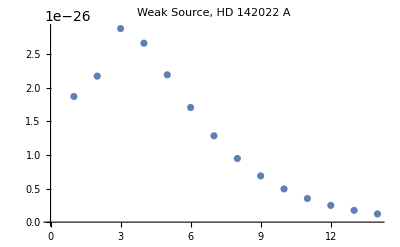

```mathematica
ListPlot[aTable[[1]], PlotLabel->"Weak Source, "<>fdata6[[ 1]][[ cols["pl_hostname"]] ] ]
```

Or with frequency on the x-axis, in units of orbital frequency.

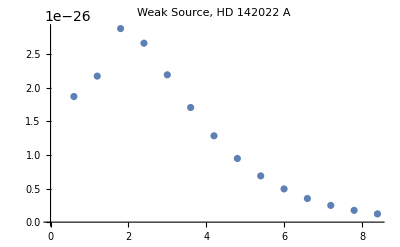

```mathematica
aData = Table[{n*aFreq, hh [n,e,m1,m2,a, dL]/.{e->fdata6[[1]][[ cols["pl_orbeccen"] ]],
m1->fdata6[[1]][[ cols["pl_bmassj"] ]]*massJ , 
m2->fdata6[[1]][[ cols["st_mass"] ]]*massSun,
a->aa,
dL->aDist}
},
{n,1,aNmax}];
plotHD142022=ListPlot[ aData, PlotLabel->"Weak Source, "<>fdata6[[ 1]][[ cols["pl_hostname"]] ] ]
```

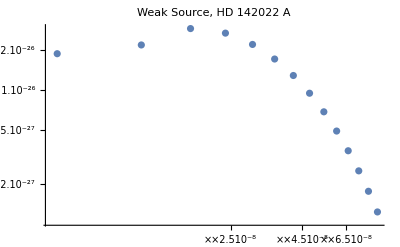

```mathematica
plotHD142022=ListLogLogPlot[ aData, PlotLabel->"Weak Source, "<>fdata6[[ 1]][[ cols["pl_hostname"]] ] ]
```

## Strain curves for LISA and eLISA

### Larson curves

```mathematica
strainDir = "/home/gabella/Documents/astro/gravWaves/LISA/strainCurves/";
strainSensLISAfile = "scg_9089LarsonLISADefs.dat"; (* with Larson defaults, 5e9 arms, etc *)
strainSensELISAfile = "scg_5412LarsonELISA1e9arm.dat";  (* just shorter arm length *)
```

```mathematica
adata = Import[strainDir<>strainSensLISAfile];
(* If first character is a # drop that data. *)
strainSensLISAdata={};
For[i=1,i≤Length[adata],i++,
If[adata[[i]][[1]]≠ "#",
strainSensLISAdata~AppendTo~adata[[i]], 
Null
]
]
strainSensLISAdata[[1;;10]] (* frequency and strain sensitiviy in per root Hz *)
```

{{9.76504×10^-8,8.23054×10^-12},{9.99256×10^-8,7.85999×10^-12},{1.02254×10^-7,7.50614×10^-12},{1.04636×10^-7,7.16821×10^-12},{1.07074×10^-7,6.84549×10^-12},{1.09569×10^-7,6.5373×10^-12},{1.12122×10^-7,6.24299×10^-12},{1.14735×10^-7,5.96193×10^-12},{1.17408×10^-7,5.69351×10^-12},{1.20144×10^-7,5.43719×10^-12}}

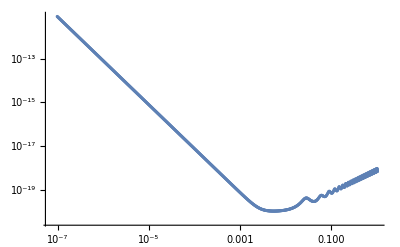

```mathematica
plotLISA=ListLogLogPlot[strainSensLISAdata, GridLines->Automatic, PlotRange->All]
```

```mathematica
adata = Import[strainDir<>strainSensELISAfile];
(* If first character is a # drop that data. *)
strainSensELISAdata={};
For[i=1,i≤Length[adata],i++,
If[adata[[i]][[1]]≠ "#",
strainSensELISAdata~AppendTo~adata[[i]], 
Null
]
]
strainSensELISAdata[[1;;10]] (* frequency and strain sensitiviy in per root Hz *)
```

{{4.88252×10^-7,1.64611×10^-12},{4.99628×10^-7,1.572×10^-12},{5.11269×10^-7,1.50123×10^-12},{5.23182×10^-7,1.43364×10^-12},{5.35372×10^-7,1.3691×10^-12},{5.47846×10^-7,1.30746×10^-12},{5.60611×10^-7,1.2486×10^-12},{5.73673×10^-7,1.19239×10^-12},{5.8704×10^-7,1.1387×10^-12},{6.00718×10^-7,1.08744×10^-12}}

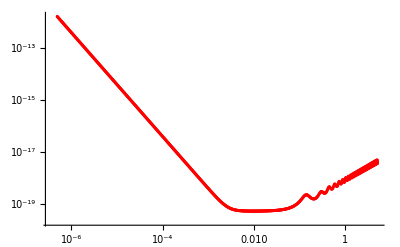

```mathematica
plotELISA=ListLogLogPlot[strainSensELISAdata, GridLines->Automatic, PlotStyle->RGBColor[1,0,0] ]
```

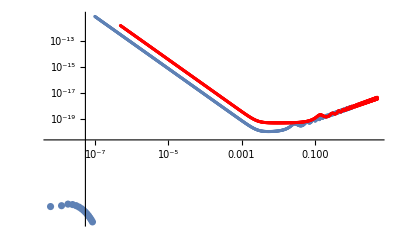

```mathematica
Show[{plotLISA,plotELISA, plotHD142022}, PlotRange->All]
```

## Now for all of the exoplanets.

Keep the organization by planet.  Data will have one entry per planet, with eccentricity, and then the frequency (in Hz) and the strain...not strain sensitivity.  Amaro-Seoane et al. and the other papers give strain.  Later there are factors for increasing the strain by numbers of cycles seen/integrated over, etc.  AS Eqn.

As in GWExopEcc2.nb, move the fdata6 data over to a set of lists of the entries.  Makes it easier to use in the forumulae.

```mathematica
Remove[aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx]
 bdata = fdata6; (* Data filtered to have non-null entries in the fields we want. *)
{aplhostname,aplorbper,aplorbsmax,aplorbeccen,aplbmassj,astdist,astmass,arowupdate,astplx}=Transpose[ bdata ]; (* List names mirror the column labels. *)
```

```mathematica
Length[bdata]
```

754

```mathematica
(* Create a list of eccen, {{freq(Hz)_1, h_1},{freq_2, h_2}....}  *)
(* fdata6 is the last filtered data, no blanks in any of my needed fields. *)
 atab=Table[
{bdata[[nn,cols["pl_orbeccen"] ]], 
Table[
Module[{afr},
afr = fr[aplbmassj[[nn]]*massJ, astmass[[nn]]*massSun, aplorbsmax[[nn]]*au];
{pp*afr, hh [pp,aplorbeccen[[nn]],aplbmassj[[nn]]*massJ,astmass[[nn]]*massSun,aplorbsmax[[nn]]*au, astdist[[nn]]*pc]}
], {pp,1,Max[ {ecc2Nmax[ aplorbeccen[[nn]] ], 3}] }
]},
{nn, 1, Length[bdata]}
];
atab[[12;;14]]//TableForm
```

0.18 | 3.52638×10^-6 | 4.69165×10^-27
7.05275×10^-6 | 3.13897×10^-26
0.0000105791 | 1.27718×10^-26
0.2 | 1.01668×10^-8 | 1.62175×10^-26
2.03336×10^-8 | 9.61035×10^-26
3.05005×10^-8 | 4.35022×10^-26
0.4 | 1.63654×10^-8 | 3.17382×10^-26
3.27308×10^-8 | 7.08011×10^-26
4.90962×10^-8 | 6.6168×10^-26
6.54616×10^-8 | 4.6313×10^-26
8.1827×10^-8 | 2.93028×10^-26
9.81924×10^-8 | 1.76275×10^-26
1.14558×10^-7 | 1.02908×10^-26

Would like just the list of frequencies and strains

```mathematica
atab[[12]][[2]]
```

{{3.52638×10^-6,4.69165×10^-27},{7.05275×10^-6,3.13897×10^-26},{0.0000105791,1.27718×10^-26}}

```mathematica
freqNstrain = {};
For[i=1,i≤Length[atab],i++,
freqNstrain~AppendTo~atab[[i]][[2]]
]
```

```mathematica
Length[freqNstrain]
```

754

```mathematica
freqNstrain[[1;;3]]
```

{{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27}},{{5.37385×10^-9,8.23435×10^-26},{1.07477×10^-8,4.50948×10^-26},{1.61216×10^-8,8.43126×10^-26},{2.14954×10^-8,9.56102×10^-26},{2.68693×10^-8,9.39107×10^-26},{3.22431×10^-8,8.63408×10^-26},{3.7617×10^-8,7.64652×10^-26},{4.29908×10^-8,6.61219×10^-26},{4.83647×10^-8,5.62442×10^-26},{5.37385×10^-8,4.72716×10^-26},{5.91124×10^-8,3.93701×10^-26},{6.44862×10^-8,3.25559×10^-26},{6.98601×10^-8,2.67671×10^-26},{7.52339×10^-8,2.19041×10^-26},{8.06078×10^-8,1.78541×10^-26},{8.59816×10^-8,1.45046×10^-26},{9.13555×10^-8,1.17498×10^-26},{9.67293×10^-8,9.49465×10^-27},{1.02103×10^-7,7.65571×10^-27},{1.07477×10^-7,6.16115×10^-27},{1.12851×10^-7,4.94994×10^-27},{1.18225×10^-7,3.9708×10^-27}},{{3.50151×10^-8,1.67249×10^-27},{7.00302×10^-8,4.48259×10^-27},{1.05045×10^-7,3.73082×10^-27},{1.4006×10^-7,2.35543×10^-27},{1.75075×10^-7,1.3482×10^-27},{2.1009×10^-7,7.34517×10^-28}}}

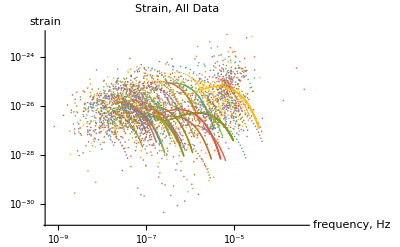

```mathematica
ListLogLogPlot[freqNstrain, PlotLabel->"Strain, All Data", AxesLabel->{"frequency, Hz", "strain"}]
```

### Enhance strain by observation time, follow A-S Eqn (10).

Multiply the strain, THE STRAIN, found above by √(n·f_r·max(T_orb,T_obs)), so if we observe for many orbital periods of the exop, it amounts, since f_(r,n)=n f_r (f_r is orbital frequency) is the GW frequency, it amounts to the square-root of the number of oscillations of the wave observed.  At this point, the peak around periapsis is just to say you get a spike every orbit, so a periodic signal.  This spike has the frequency content  mentioned above g[n,e] for the n-th harmonic.

```mathematica
fobs[n_,fr_,Tobs_]:=√(n Max[1,fr*Tobs]) (* AS Eqn (10) for long observation. *)
```

So fix up the data with above factor.

```mathematica
freqNstrain[[1]]
```

{{5.99455×10^-9,1.87098×10^-26},{1.19891×10^-8,2.17487×10^-26},{1.79836×10^-8,2.88323×10^-26},{2.39782×10^-8,2.66585×10^-26},{2.99727×10^-8,2.19441×10^-26},{3.59673×10^-8,1.70757×10^-26},{4.19618×10^-8,1.2859×10^-26},{4.79564×10^-8,9.4794×10^-27},{5.39509×10^-8,6.88467×10^-27},{5.99455×10^-8,4.94559×10^-27},{6.594×10^-8,3.52291×10^-27},{7.19345×10^-8,2.49289×10^-27},{7.79291×10^-8,1.75458×10^-27},{8.39236×10^-8,1.22948×10^-27}}

```mathematica
Length[freqNstrain]
```

754

```mathematica
Tobs=10.0*secsYear;  (* 10 year observing *)
```

```mathematica
freqNstrain2={};
For[i=1,i≤Length[freqNstrain],i++,
aa = freqNstrain[[i]];
freqNstrain2~AppendTo~
Table[{aa[[j,1]],aa[[j,2]]*fobs[j, aa[[1,1]],Tobs]},
{j, 1, Length[aa]} ]
]
```

```mathematica
{Tobs,1/Tobs, 1/(5.99 10^-9), 5.99 10^-9*Tobs,√(5.99455 10^-9*Tobs), √(5.99455 10^-9*Tobs*14)}
```

{3.15567×10^8,3.1689×10^-9,1.66945×10^8,1.89025,1.37539,5.14622}

```mathematica
{1.375*1.871, 1.23*5.146}
```

{2.57263,6.32958}

```mathematica
freqNstrain2[[1]]
```

{{5.99455×10^-9,2.57331×10^-26},{1.19891×10^-8,4.23032×10^-26},{1.79836×10^-8,6.86853×10^-26},{2.39782×10^-8,7.33314×10^-26},{2.99727×10^-8,6.74881×10^-26},{3.59673×10^-8,5.75278×10^-26},{4.19618×10^-8,4.67929×10^-26},{4.79564×10^-8,3.68765×10^-26},{5.39509×10^-8,2.84072×10^-26},{5.99455×10^-8,2.15101×10^-26},{6.594×10^-8,1.60702×10^-26},{7.19345×10^-8,1.18773×10^-26},{7.79291×10^-8,8.70101×10^-27},{8.39236×10^-8,6.32718×10^-27}}

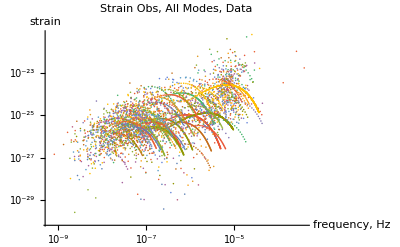

```mathematica
plotStrainObs=ListLogLogPlot[freqNstrain2, PlotLabel->"Strain Obs, All Modes, Data", AxesLabel->{"frequency, Hz", "strain"}]
```

### Back to Larson Strain Sensitivity and convert to Strain.

#### Observation time, divide by root(Tobs).

```mathematica
TLISAObs=10*secsYear; (* seconds *)
Module[{afreq,aLISA, aLISAnew},
{afreq,aLISA} = Transpose[strainSensLISAdata ];
aLISAnew = aLISA/√TLISAObs;
strainLISAdataTobs=Transpose[{afreq,aLISAnew}];
]
Module[{afreq,aLISA, aLISAnew},
{afreq,aLISA} = Transpose[strainSensELISAdata ];
aLISAnew = aLISA/√TLISAObs;
strainELISAdataTobs=Transpose[{afreq,aLISAnew}];
]
```

```mathematica
(*strainSensLISAdata*)
```

```mathematica
(*strainLISAdata1sec*)
```

```mathematica
{Tobs, √Tobs,1/√Tobs}
```

{3.15567×10^8,17764.2,0.0000562929}

```mathematica
Sens
```

Sens

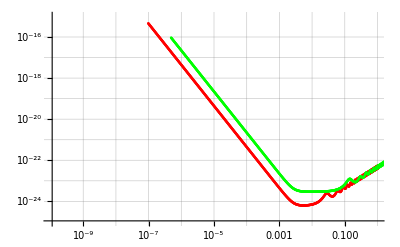

```mathematica
(* GridLines->Automatic *)plotTobs=ListLogLogPlot[{strainLISAdataTobs,strainELISAdataTobs}, GridLines->{Table[10^ii//N, {ii, -9, 0, 1}], Table[10^ii//N, {ii, -24, -16, 1}]}, PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0]}, PlotRange->{{10^-10,10^0},{10^-25,10^-15}} ]
```

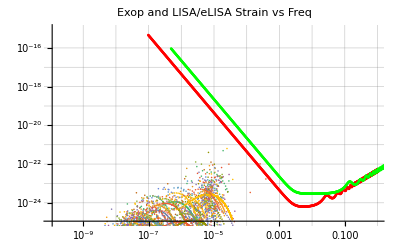

```mathematica
Show[{plotTobs, plotStrainObs}, PlotLabel->"Exop and LISA/eLISA Strain vs Freq"]
```

less scg_9089LarsonLISADefs.dat
# For this data file:
# SNR = 1.000000 
# Armlength = 5.000000e+09      meters
# Optics diameter = 0.300000    meters
# Wavelength = 1064.000000      nanometers
# Laser power = 1.000000 Watts
# Optical train efficiency = 0.300000 
# Accleration noise = 3.000000e-15 m/(s^2 root Hz)   <<<< eLISA Pathfinder measured about 5.5e-15 m/s^2 per root Hz.
# Position noise = 2.000000e-11 m/(root Hz)
# Sensitivity Floor Set by Position Noise Budget
# Output Curve type is Root Spectral Density, per root Hz
# Astrophysical Noise is No White Dwarf Noise

## Bin the data into about 10-ish bins in frequency, even in log-space.

Flatten the scaled up strain and frequency, and remove any 0 entries for strain (like for circular orbits, n=1,3 are zero).

```mathematica
dataFlat = Flatten[ freqNstrain2, 1];
Print["Length of dataFlat is "<>ToString[ Length[dataFlat] ]<>"."]
dataFlatFiltered = {};
For[ii=1, ii≤Length[dataFlat], ii++, 
If[dataFlat[[ii,2]]==0, , AppendTo[dataFlatFiltered, dataFlat[[ii]] ] ];
];
Print["Length of aflatFiltered  is "<>ToString[ Length[dataFlatFiltered ] ]<>"."]
```

Length of dataFlat is 5447.

Length of aflatFiltered  is 5189.

Save only those above some limit, like 1e-6 Hz.

```mathematica
Clear[saveBigData]  (* For a pair of data {{freq1,hfs1}, {freq2,hfs2}...} *)
saveBigData[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]][[1]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

```mathematica
Clear[saveBig]  (* Not so necessary, when you check inBin that will filter out the low stuff. *)
saveBig[alist_] := Module[{aa={},bb, alim=10^-6},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥alim, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

Add the amplitudes in the list as root-mean-squares.

```mathematica
Clear[addLikeRMS];
addLikeRMS[a_]:=Sqrt[ Sum[a[[i]]^2,{i,1,Length[a]} ] ]
```

Find those frequencies in the bin for RMS addition.

```mathematica
Clear[inBin]
inBin[alist_,lower_,upper_] := Module[{aa={}},
For[i=1, i<=Length[alist], i++,
If[alist[[i]]≥lower && alist[[i]]<upper, AppendTo[aa,alist[[i]]], ];
];
aa
]
```

Binsize log-space 0.130103 No. bin boundaries 21

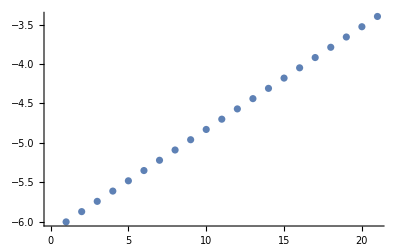

```mathematica
amin=Log10[1. 10^-6];
amax=Log10[4. 10^-4];
nBins = 20;
myBins={Table[amin+(amax-amin)*i/nBins,{i,0,nBins}]}; (* Evenly spaced in log-space. *)
Print["Binsize log-space ",(amax-amin)/nBins//N, " No. bin boundaries ", Length[myBins[[1]] ] ]
ListPlot[myBins]
```

```mathematica
freqNstrain2[[1;;2]] (* still organized by planet, lose this *)
```

{{{5.99455×10^-9,2.57331×10^-26},{1.19891×10^-8,4.23032×10^-26},{1.79836×10^-8,6.86853×10^-26},{2.39782×10^-8,7.33314×10^-26},{2.99727×10^-8,6.74881×10^-26},{3.59673×10^-8,5.75278×10^-26},{4.19618×10^-8,4.67929×10^-26},{4.79564×10^-8,3.68765×10^-26},{5.39509×10^-8,2.84072×10^-26},{5.99455×10^-8,2.15101×10^-26},{6.594×10^-8,1.60702×10^-26},{7.19345×10^-8,1.18773×10^-26},{7.79291×10^-8,8.70101×10^-27},{8.39236×10^-8,6.32718×10^-27}},{{5.37385×10^-9,1.0723×10^-25},{1.07477×10^-8,8.30482×10^-26},{1.61216×10^-8,1.9017×10^-25},{2.14954×10^-8,2.49013×10^-25},{2.68693×10^-8,2.73457×10^-25},{3.22431×10^-8,2.7541×10^-25},{3.7617×10^-8,2.63452×10^-25},{4.29908×10^-8,2.43545×10^-25},{4.83647×10^-8,2.19729×10^-25},{5.37385×10^-8,1.94665×10^-25},{5.91124×10^-8,1.7004×10^-25},{6.44862×10^-8,1.46862×10^-25},{6.98601×10^-8,1.25679×10^-25},{7.52339×10^-8,1.06728×10^-25},{8.06078×10^-8,9.00479×10^-26},{8.59816×10^-8,7.55535×10^-26},{9.13555×10^-8,6.30876×10^-26},{9.67293×10^-8,5.24571×10^-26},{1.02103×10^-7,4.34562×10^-26},{1.07477×10^-7,3.58811×10^-26},{1.12851×10^-7,2.95392×10^-26},{1.18225×10^-7,2.42537×10^-26}}}

```mathematica
freqNstrainFlat = Flatten[freqNstrain2,1]; (* Flatten only one level. *)
freqNstrainFlat[[1;;4]]
Length[freqNstrainFlat]
```

{{5.99455×10^-9,2.57331×10^-26},{1.19891×10^-8,4.23032×10^-26},{1.79836×10^-8,6.86853×10^-26},{2.39782×10^-8,7.33314×10^-26}}

5447

```mathematica
{freq,strain}=Transpose[freqNstrainFlat];
```

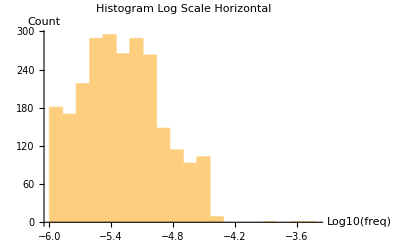

Binsize dLog  0.130103  10^amin  1.×10^-6  multiple 10^dLog  1.34928

```mathematica
Histogram[Log10[freq],myBins, PlotRange->All,
PlotLabel->"Histogram Log Scale Horizontal",
AxesLabel->{"Log10(freq)","Count"}]
(*Histogram[ Log10[freqsBig]]*)
Print["Binsize dLog  ",aa=(amax-amin)/nBins//N, "  10^amin  ", 10^amin//N,"  multiple 10^dLog  ", 10^aa]
```

Bin the aflatBig.  2D version of BinLists looks like the right way to go.  The second dimension is {{-Infinity,Infinity}} for the binning, this also adds an extra set of parentheses.

```mathematica
(* use myBins, in the log-space of freqency from 1e-6 to 4e-4 Hz *)
{freq, hstrain}=Transpose[freqNstrainFlat];
freqNstrainLogFreq = Transpose[ {Log10[freq],hstrain}];
freqNstrainBL=BinLists[freqNstrainLogFreq,myBins,{{-∞,+∞}}];
```

```mathematica
{Length[freqNstrainBL], Length[freqNstrainBL[[1,1]] ]} (* Now a list of 20 lists each in the respective bin. These are log frequencies. *)
```

{20,181}

```mathematica
{ Length[myBins[[1]]], Length[freqNstrainBL] }
```

{21,20}

Use the Center of the bin for the position in frequency space.

```mathematica
freqNstrainRMS = {};
For[i=1,i≤Length[freqNstrainBL], i++,
Module[{afreq, afreqLog, astrain, astrainRMS},
(*Print["i is ",i," Length afreqLog astrain  freqNstrainBL[[i,1]] ",Length[afreqLog],"  ", Length[astrain], "  ",Length[freqNstrainBL[[i,1]] ] ] ;*)
If[ Length[freqNstrainBL[[i,1]] ] ≠ 0,
{afreqLog, astrain}=Transpose[freqNstrainBL[[i,1]] ];,
astrain = 0.0;
];
afreq = ( myBins[[1,i]]+myBins[[1,i+1]] )/2;
astrainRMS = addLikeRMS[astrain];
freqNstrainRMS ~AppendTo~ { 10^afreq, astrainRMS};
]
]
```

i is 1 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  181

i is 2 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  170

i is 3 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  218

i is 4 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  289

i is 5 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  295

i is 6 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  265

i is 7 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  289

i is 8 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  263

i is 9 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  148

i is 10 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  114

i is 11 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  93

i is 12 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  103

i is 13 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  9

i is 14 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  0

i is 15 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  0

i is 16 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  0

i is 17 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  1

i is 18 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  0

i is 19 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  1

i is 20 Length afreqLog astrain  freqNstrainBL[[i,1]] 0  0  1

```mathematica
freqNstrainRMS
```

{{1.16159×10^-6,2.04678×10^-23},{1.56731×10^-6,6.70731×10^-23},{2.11474×10^-6,2.18199×10^-23},{2.85339×10^-6,1.52568×10^-22},{3.85002×10^-6,1.15412×10^-22},{5.19477×10^-6,9.08307×10^-23},{7.00922×10^-6,4.36342×10^-22},{9.45742×10^-6,1.84335×10^-22},{0.0000127607,8.18081×10^-23},{0.0000172178,5.01019×10^-22},{0.0000232317,6.33546×10^-22},{0.0000313462,1.03662×10^-22},{0.0000422949,1.60622×10^-23},{0.0000570677,0},{0.0000770005,0},{0.000103895,0},{0.000140184,3.40829×10^-24},{0.000189148,0},{0.000255215,1.02614×10^-22},{0.000344357,1.6974×10^-23}}

```mathematica
(* PlotMarkers   Graphics[{Blue,Circle[]}] "○"   *)
```

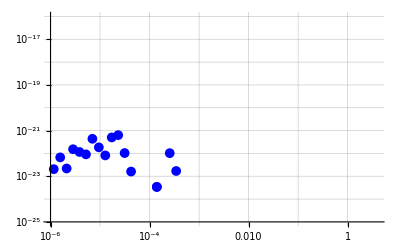

```mathematica
plotBinned=ListLogLogPlot[freqNstrainRMS,
PlotRange->{{10^-6,4},{10^-25,10^-16}},AxesOrigin->{10^-6,10^-25}, 
GridLines->{Table[10^ii//N, {ii, -9, 0, 1}], Table[10^ii//N, {ii, -24, -16, 1}]},
PlotMarkers->{ Graphics[{Blue,Disk[]}, ImageSize->10] },
PlotStyle->{RGBColor[0,0,1],PointSize[0.03]} 
]
```

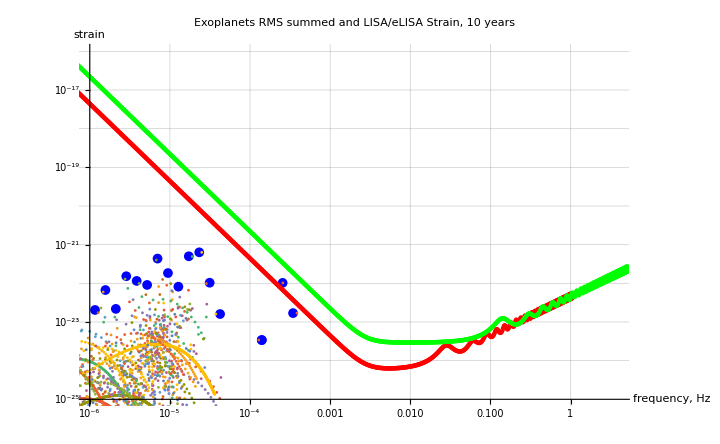

thePlot.pdf

thePlot.png

```mathematica
plotTheOne=Show[{plotBinned, plotTobs, plotStrainObs}, 
(*PlotRange->{{10^-6,4},{10^-25,10^-16}},AxesOrigin->{10^-6,10^-25},*)
PlotLabel->"Exoplanets RMS summed and LISA/eLISA Strain, 10 years",
LabelStyle->Directive[Black,AbsoluteThickness[1],18,FontFamily->"Helvetica"],
AxesLabel->{"frequency, Hz", "strain"},
AxesStyle->Directive[Black,AbsoluteThickness[1],18,FontFamily->"Helvetica"],ImageSize->720
]
Export[ "thePlot.pdf",plotTheOne]
Export["thePlot.png", plotTheOne]
```